Вариант 7 Логаш Полина

1

1) Задаем начальные данные

```mathematica
X={0., π/6,π/4,π/3,π/12};
f[x_]=Tan[x]^2;
n=Length[X]-1;
Do[{Subscript[x, i]=X[[i+1]],Subscript[f, i]=f[Subscript[x, i]]},{i,0,n}]
```

2) Строим алгебраический интерполяционный многочлен через определитель

```mathematica
Unprotect[Power];
0^0:=1;
Do[Subscript[fi, j][x_]=x^j,{j,0,n}];
Do[Subscript[d, i,j]=Subscript[fi, j][Subscript[x, i]],{i,0,n},{j,0,n}];
Do[{Subscript[d, i,n+1]=Subscript[f, i],Subscript[d, n+1,i]=Subscript[fi, i][x]},{i,0,n}];
Subscript[d, n+1,n+1]=0;
V=Table[Subscript[d, i,j],{i,0,n},{j,0,n}];
V1=Table[Subscript[d, i,j],{i,0,n+1},{j,0,n+1}];
%//MatrixForm
P[x_]=-Det[V1]/Det[V]//Expand
```

(1 | 0. | 0. | 0. | 0. | 0.
1 | π/6 | π^2/36 | π^3/216 | π^4/1296 | 1/3
1 | π/4 | π^2/16 | π^3/64 | π^4/256 | 1
1 | π/3 | π^2/9 | π^3/27 | π^4/81 | 3
1 | π/12 | π^2/144 | π^3/1728 | π^4/20736 | (2-√3)^2
1 | x | x^2 | x^3 | x^4 | 0)

0.-0.494576 x+4.5796 x^2-7.93074 x^3+6.32251 x^4

3) Строим алгебраический интерполяционный многочлен с помощью функции InterpolatingPolynomial для проверки полученного результата :

```mathematica
Tbl=Table[{Subscript[x, i],Subscript[f, i]},{i,0,n}];
P1[x_]=InterpolatingPolynomial[Tbl,x]//Expand
```

0.-0.494576 x+4.5796 x^2-7.93074 x^3+6.32251 x^4

3.2) Сравниваем интерполяционные многочлены :

```mathematica
((P[x]-P1[x])//Chop)==0
```

True

3.3) Проверяем выполнение интерполяционных условий :

```mathematica
Table[((P[Subscript[x, i]]-Subscript[f, i])//Chop)==0,{i,0,n}]
```

{True,True,True,True,True}

4) Изображаем = исходную систему точек, заданную функцию и полученный
интерполяционный многочлен в одной системе координат :

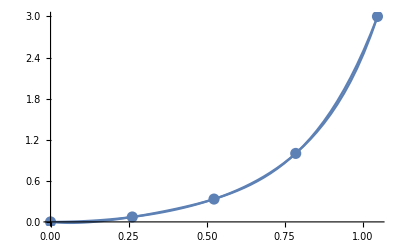

```mathematica
Gr1=ListPlot[Tbl,PlotStyle->{PointSize[0.02]}];
Gr2=Plot[P[x],{x,Min[X],Max[X]}];
Gr3=Plot[f[x],{x,Min[X],Max[X]}];
Show[Gr1,Gr2,Gr3]
```

5) Находим приближенное значение f(x) при указанном аргументе:

```mathematica
SuperStar[x]=π/9;
P[SuperStar[x]]
```

0.141924

6) Приближенное значение сравниваем с точным значением функции (находим абсолютную и относительную погрешность приближения) :

```mathematica
A=N[Abs[f[SuperStar[x]]-P[SuperStar[x]]],2]
B=N[A/(P[SuperStar[x]]//Abs)*100,2]
```

0.00944947

6.65813

2

Доказываем, что функции на функции 1, cos x на отрезке [-π/2,π/2] линейно
независимы, но системы Чебышева не образуют.

```mathematica
Subscript[t, 0]=-π/2;
Subscript[t, 1]=π/2;
Det[Table[{1,Cos[Subscript[t, j]]},{j,0,1}]]==0
```

True

1) Функции 1 и cos(x) являются линейно независимыми так как α*1+β*cos(x) = 0 ⇔ когда α = 0 и β = 0
2) Так как для различных t_0, t_1∈ [-π/2,π/2] определитель равен 0, то по теореме об необходимом и достаточном условии для того, чтобы система функций была Чебышевской не выполняется необходимое условие, следовательно система функций 1 и cos(x) не являестя Чебышевской на [-π/2,π/2]